```mathematica
img0=Binarize[-Graphics-]
```

-Graphics-

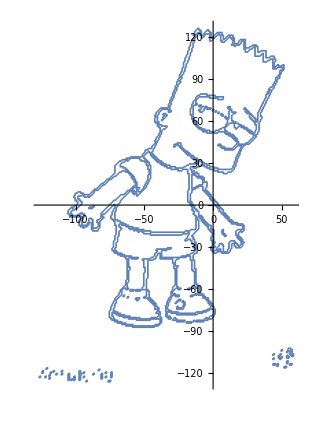

```mathematica
img=Binarize[img0~ColorConvert~"Grayscale"~ImageResize~190~Blur~0,.15];
img=DeleteSmallComponents@img;

pts=DeleteDuplicates@Flatten[Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[All,1]],1];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=#-center&/@pts;
plot=ListPlot[pts,AspectRatio->Automatic,PlotRange->Full]
```

```mathematica
shortest=Last@FindShortestTour@pts;
pts=pts[[shortest]];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of pts⟦pts⟧.

```mathematica
Export["Ptos.txt",pts]
```

Ptos.txt

```mathematica
Import["Ptos.txt"]
```

--------------------------------------------This is the directory you need to use in the python code.---------------------------------------------------

```mathematica
ExpandFileName["Ptos.txt"]
```

C:\Users\renec\OneDrive\Documentos\Ptos.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Ptos.txt"]]]
```